#### Step H: Histogram plots

```mathematica
filenameVolumeBase="FR96D1_"; 
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

{309,566,374}

```mathematica
100*Max[concFR]
```

7.07778

```mathematica
SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFR],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{4244.,Null}

60108823

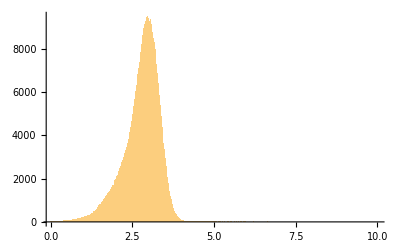

2.77894

0.53676

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,10,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
(*______________________________________*)
```

```mathematica
filenameVolumeBase="FR96D1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

```mathematica
Dimensions[concSb2O3]
100*Max[concSb2O3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3],#>0&];//Timing
Length[listOfNonZeroVoxels]
```

{309,566,374}

10.5528

{1089.36,Null}

57909428

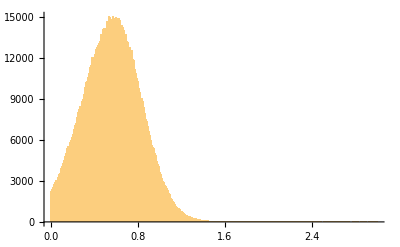

0.571131

0.273197

```mathematica
Histogram[RandomSample[100*listOfNonZeroVoxels,1000000],{0.0,3,0.01}]
100*Mean[listOfNonZeroVoxels]
100*StandardDeviation[listOfNonZeroVoxels]
```

```mathematica
--------------------------------------------------------------------------------------
```

```mathematica
(*concFR=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFR]*)
```

```mathematica
(*100*Max[concFR]
```

```mathematica
(*SeedRandom[1];
Histogram[RandomSample[100*Flatten[concFR],100000],{1.0,8,0.1}]*)
```

```mathematica
(*sliceFR = Take[concFR,{128},{300,600},{600,800}];
sliceFR = Take[concFR,{128},{400,600},{400,700}];
Dimensions[sliceFR]
sliceFR =sliceFR[[1]];
Dimensions[sliceFR]
Image[sliceFR,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceFR],{0.0,10,0.1}]*)
```

```mathematica
(*concSb2O3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3]*)
```

```mathematica
(*100*Max[concSb2O3]*)
```

```mathematica
(*sliceSb2O3 = Take[concSb2O3,{128},{300,600},{600,800}];
sliceSb2O3 = Take[concSb2O3,{128},{400,600},{400,700}];
Dimensions[sliceSb2O3]
sliceSb2O3 =sliceSb2O3[[1]];
Dimensions[sliceSb2O3]
Image[sliceSb2O3,"Real32"]//ImageAdjust
Histogram[100*Flatten[sliceSb2O3],{0.1,2,0.1}]
100*Max[sliceSb2O3]*)
```

```mathematica
(*dataFRandSb2O3 = Transpose[{100*Flatten[sliceFR],100*Flatten[sliceSb2O3]}];
Dimensions[dataFRandSb2O3]
Histogram3D[dataFRandSb2O3,{{0.1,10,0.1},{0.1,2,0.05}},ChartElementFunction->"GradientScaleCube"]*)
```

FOR BFR PLOTS

```mathematica
filenameVolumeBase="FR96D3_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concFRD3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_374_374_492_new.h5",{"Datasets","concFR"}];
Dimensions[concFRD3]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

{492,374,374}

```mathematica
filenameVolumeBase="FR96D1_";
concFRD1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRD1]
```

{309,566,374}

```mathematica
filenameVolumeBase="FR96C1_";
concFRC1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRC1]
```

{250,400,560}

```mathematica
filenameVolumeBase="FR96B1_";
concFRB1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRB1]
```

{200,350,500}

```mathematica
(*filenameVolumeBase="FR96D2_";
concFRD2=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRD2]*)
```

{256,310,560}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concFRD3],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD3 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFRD1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRC1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRC1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRC1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRB1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRB1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRB1]
```

{111.827,Null}

68812901

1000000

{128.763,Null}

60108823

1000000

{136.686,Null}

51173252

1000000

{121.285,Null}

32253739

1000000

```mathematica
(*SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRD2],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD2 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD2]*)
```

{118.551,Null}

68812901

1000000

{176.942,Null}

45628433

1000000

{141.564,Null}

30034282

1000000

{90.5652,Null}

31993721

1000000

{82.2675,Null}

25823850

1000000

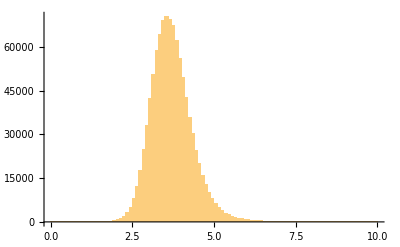

3.71148

0.667569

```mathematica
Histogram[concFRD3,{0.0,10,0.1}]
Mean[concFRD3]
StandardDeviation[concFRD3]
```

```mathematica
list =HistogramList[concFRD3,{0.0,100,0.1}];
threshold=5.1;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

52

150983.

3.71149×10^6

4.06798

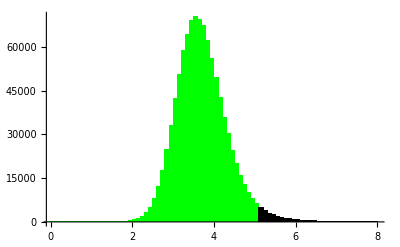

```mathematica
listBelowThreshold = Histogram[Select[concFRD3,#<threshold &],{0.0,8,0.1},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concFRD3,#>=threshold &],{0,8,0.1},ChartStyle->Directive[Black,EdgeForm[]]];
gFRD3=Show[{listBelowThreshold,listAboveThreshold}]
```

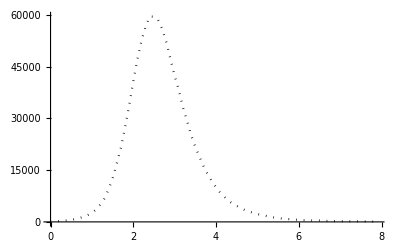

```mathematica
data =HistogramList[concFRB1,{0,8,0.1}];
gFRB1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]]
```

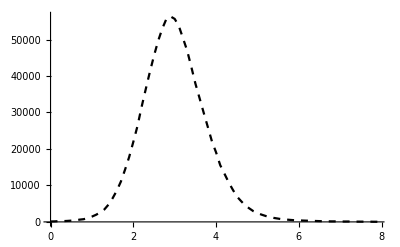

```mathematica
data =HistogramList[concFRC1,{0,8,0.1}];
gFRC1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]]
```

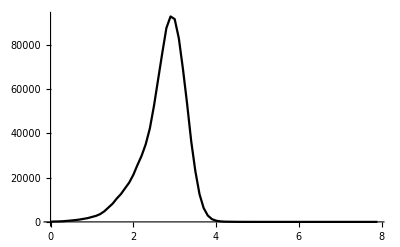

```mathematica
data =HistogramList[concFRD1,{0,8,0.1}];
gFRD1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]]
```

```mathematica
(*data =HistogramList[concFRD2,{0,8,0.1}];
gFRD2 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Purple,Thick]]*)
```

```mathematica
{gFRB1,gFRC1,gFRD1}
```

{-Graphics-,-Graphics-,-Graphics-}

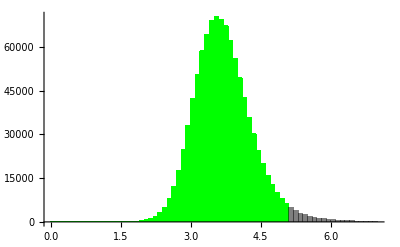

```mathematica
gHistD3=Histogram[{
Select[concFRD3,#<threshold &],
Select[concFRD3,#>=threshold &]},{0,7,.1},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

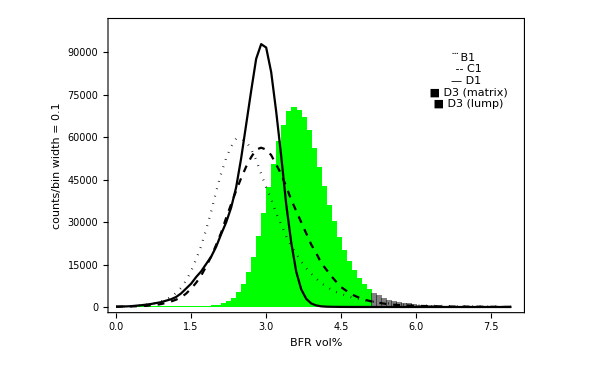

{54.6997,Null}

65109344

1000000

```mathematica
Show[{gHistD3,gFRD1,gFRB1,gFRC1},PlotRange->{{0,8},{0,100000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ B1\n -- C1\n— D1\n ■ D3 (matrix)\n ■ D3 (lump)"],{7.0,80000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"B1", Mean[concFRB1],StandardDeviation[concFRB1],Max[concFRB1]},
{"C1", Mean[concFRC1],StandardDeviation[concFRC1],Max[concFRC1]},
{"D1", Mean[concFRD1],StandardDeviation[concFRD1],Max[concFRD1]},
{"D3", Mean[concFRD3],StandardDeviation[concFRD3],Max[concFRD3]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"D3", threshold,fractionBFRinlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
B1 | 2.77188 | 0.860319 | 15.0531
C1 | 3.05363 | 0.802023 | 17.0422
D1 | 2.77898 | 0.537072 | 6.6423
D3 | 3.71148 | 0.667569 | 29.0579

sample | threshold | fraction in lumps
D3 | 5.1 | 4.06798

Sb2O3 plots

```mathematica
filenameVolumeBase="FR96D3_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/"
concSb2O3D3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_374_374_492_new.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3D3]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/

{492,374,374}

```mathematica
filenameVolumeBase="FR96D1_";
concSb2O3D1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3D1]
```

{256,545,670}

```mathematica
filenameVolumeBase="FR96C1_";
concSb2O3C1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3C1]
```

{205,587,650}

```mathematica
filenameVolumeBase="FR96A1_";
concSb2O3A1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3A1]
```

{300,318,500}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concSb2O3D3],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3D3 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3D3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3D1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3D1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3D1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3C1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3C1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3C1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3A1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3A1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3A1]
```

{122.877,Null}

65615714

1000000

{183.014,Null}

45005703

1000000

{196.062,Null}

24672347

1000000

{75.9285,Null}

47533860

1000000

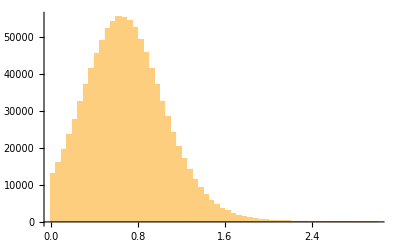

0.705701

0.38607

```mathematica
Histogram[concSb2O3D3,{0.0,3,0.05}]
Mean[concSb2O3D3]
StandardDeviation[concSb2O3D3]
```

```mathematica
list =HistogramList[concSb2O3D3,{0.0,100,0.05}];
threshold=1.4;  (* based on D3 *)
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionSb2O3inlumps = 100*volPercentNumerator/volPercentDenominator
```

29

62875.6

705782.

8.90865

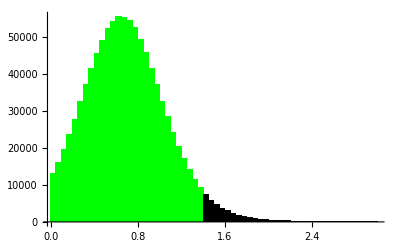

```mathematica
listBelowThreshold = Histogram[Select[concSb2O3D3,#<threshold &],{0,3,0.05},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concSb2O3D3,#>=threshold &],{0,3,0.05},ChartStyle->Directive[Black,EdgeForm[]]];
gSb2O3D3=Show[{listBelowThreshold,listAboveThreshold}]
```

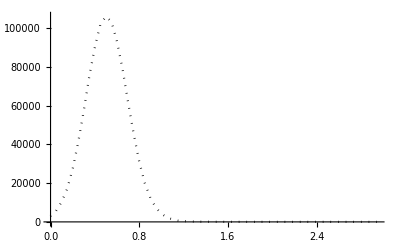
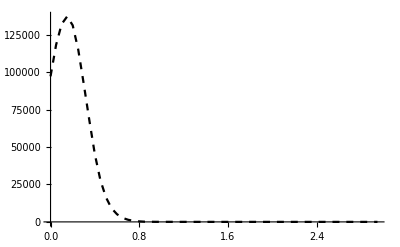
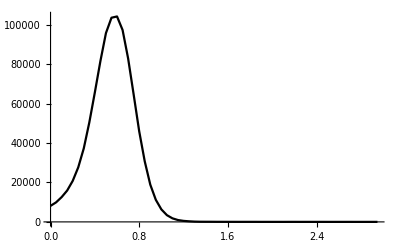

```mathematica
data =HistogramList[concSb2O3A1,{0,3,0.05}];
gSb2O3A1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concSb2O3C1,{0,3,0.05}];
gSb2O3C1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concSb2O3D1,{0,3,0.05}];
gSb2O3D1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gSb2O3A1,gSb2O3C1,gSb2O3D1}
```

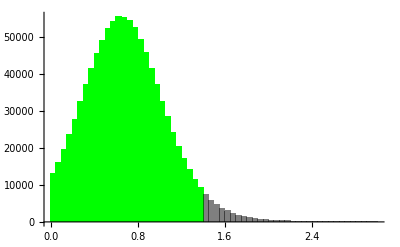

```mathematica
gHistD3=Histogram[{
Select[concSb2O3D3,#<threshold &],
Select[concSb2O3D3,#>=threshold &]},{0,3,0.05},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

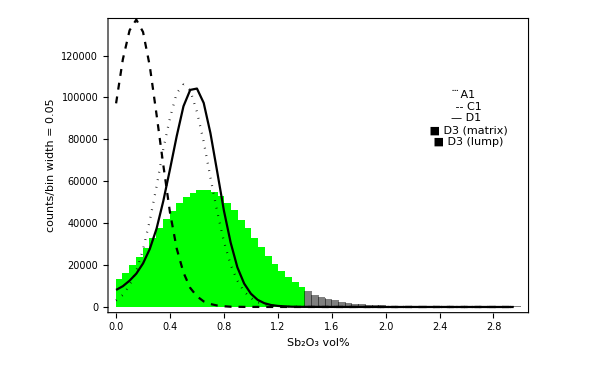

```mathematica
Show[{gHistD3,gSb2O3D1,gSb2O3A1,gSb2O3C1},PlotRange->{{0,3},{0,135000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.05",""},{"Sb_2O_3 vol%",""}},
Epilog->Style[Text[Framed[" ⃛ A1\n -- C1\n— D1\n ■ D3 (matrix)\n ■ D3 (lump)"],{2.6,90000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"A1", Mean[concSb2O3A1],StandardDeviation[concSb2O3A1],Max[concSb2O3A1]},
{"C1", Mean[concSb2O3C1],StandardDeviation[concSb2O3C1],Max[concSb2O3C1]},
{"D1", Mean[concSb2O3D1],StandardDeviation[concSb2O3D1],Max[concSb2O3D1]},
{"D3", Mean[concSb2O3D3],StandardDeviation[concSb2O3D3],Max[concSb2O3D3]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"D3", threshold,fractionSb2O3inlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
A1 | 0.536193 | 0.193723 | 10.0555
C1 | 0.222082 | 0.144883 | 8.70337
D1 | 0.575726 | 0.208987 | 11.6758
D3 | 0.705701 | 0.38607 | 14.0064

sample | threshold | fraction in lumps
D3 | 1.4 | 8.90865